```mathematica
gamma={KroneckerProduct[PauliMatrix[3],PauliMatrix[2]],KroneckerProduct[PauliMatrix[3],PauliMatrix[3]],KroneckerProduct[PauliMatrix[2],PauliMatrix[0]],KroneckerProduct[PauliMatrix[3],PauliMatrix[1]],KroneckerProduct[PauliMatrix[1],PauliMatrix[0]]}; (* Indices from 1 to 5, gamma_0 = gamma[[4]] *)
```

```mathematica
pPlus=(IdentityMatrix[4]+gamma[[3]])/2;
pMinus=(IdentityMatrix[4]-gamma[[3]])/2;
```

```mathematica
largeB={bb->1/(2b Sinh[α])};
alpha={α->ArcCosh[(1+b^2+Total[Sin[p]^2])/(2b)]};
smallB={b->1-mm+Total[1-Cos[p]]};
pSlash={pS->p[[1]]gamma[[4]]+p[[2]]gamma[[1]]+p[[3]]gamma[[2]]};
momentum={p->{p0,p1,p2}};
```

Part::partd: Part specification p⟦1⟧ is longer than depth of object.

Part::partd: Part specification p⟦2⟧ is longer than depth of object.

Part::partd: Part specification p⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

```mathematica
Δ[m_,index_]:=Exp[2α](b-Exp[-α])+m^2(Exp[α]-b)+If[index==3,0,Exp[-α(Ls-1)]4m b Sinh[α]]+Exp[-2α(Ls-1)](m^2(b-Exp[-α])+Exp[-2α](Exp[α]-b))
aPlus[m_,index_]:=bb(Exp[α]-b)(1-m^2)/Δ[m,index]
aMinus[m_,index_]:=bb(Exp[-α]-b)(1-m^2)/Δ[m,index]
aM[m_,index_]:=bb(-2m b Sinh[α]If[index==3,I,1]+Exp[-α(Ls-1)](Exp[-2α](b-Exp[α])+m^2(Exp[-α]-b)))/Δ[m,index]
greens[s_,m_,index_]:=IdentityMatrix[4]bb*Exp[-α If[s[[2]]==Ls,s[[2]]-s[[1]],s[[1]]-s[[2]]]]+(pPlus aPlus[m,index]+pMinus aMinus[m,index])*Exp[-α(s[[2]]+s[[1]]-2)]+(pPlus aMinus[m,index]+pMinus aPlus[m,index])*Exp[-α(2Ls-s[[2]]-s[[1]])]+IdentityMatrix[4]aM[m,index](Exp[-α(Ls-s[[2]]+s[[1]]-1)]+Exp[-α(Ls+s[[2]]-s[[1]]-1)])
```

```mathematica
dDaggerG[s_,m_,index_]:=-pPlus.greens[{2,s},m,index]+b greens[{1,s},m,index]+m pMinus.greens[{Ls,s},m,index]
pMdDaggerG[s_,m_,index_]:=b pMinus.greens[{1,s},m,index]+m pMinus.greens[{Ls,s},m,index]
g0pMdDaggerG[s_,m_,index_]:=-I Sin[p[[1]]] pPlus.greens[{1,s},m,index]
```

```mathematica
corr001[m_,x_]:=Evaluate[Tr[g0pMdDaggerG[1,m,1]]/.Ls->Log[1/x]/α//Simplify]
corr0L1[m_,x_]:=Evaluate[Tr[pMdDaggerG[Ls,m,1]]/.Ls->Log[1/x]/α//Simplify]
corr003[m_,x_]:=Evaluate[Tr[g0pMdDaggerG[1,m,3]]/.Ls->Log[1/x]/α//Simplify]
corr0L3[m_,x_]:=Evaluate[Tr[pMdDaggerG[Ls,m,3]]/.Ls->Log[1/x]/α//Simplify]
```

```mathematica
Tr@pMdDaggerG[1,m,3]//FullSimplify
```

Piecewise[{{(b bb ⅇ^(-(2+Ls) α) (-1+ⅇ^(2 α)) (-ⅇ^(Ls α) m+ⅇ^((2+Ls) α) m+b ⅇ^α (-1+ⅇ^(2 Ls α)-2 ⅈ ⅇ^(Ls α) m)+ⅇ^(2 α) (1-(1+ⅈ) m^2)+ⅇ^(2 Ls α) (-1+(1-ⅈ) m^2)))/((-1+m^2) Sinh[Ls α]+b (m^2 Sinh[α-Ls α]+Sinh[α+Ls α])), Ls≠1}, {(4 b bb (b+m) (-ⅈ m+Sinh[α]))/(-1+m^2+2 b Cosh[α]), True}}]

```mathematica
cP001[m_,x_,p0_]:=Evaluate[corr001[m,x]/.largeB/.alpha/.smallB/.p->{p0,0,0}/.mm->1//Simplify]
cP0L1[m_,x_,p0_]:=Evaluate[corr0L1[m,x]/.largeB/.alpha/.smallB/.p->{p0,0,0}/.mm->1//Simplify]
cP003[m_,x_,p0_]:=Evaluate[corr003[m,x]/.largeB/.alpha/.smallB/.p->{p0,0,0}/.mm->1//Simplify]
cP0L3[m_,x_,p0_]:=Evaluate[corr0L3[m,x]/.largeB/.alpha/.smallB/.p->{p0,0,0}/.mm->1//Simplify]
```

```mathematica
cT001[m_,x_,t_,Lt_]:=Sum[cP001[m,x,p0]Exp[I t p0]/.p0->2Pi(n+1/2)/Lt//N,{n,0,Lt-1}]/Lt
cT0L1[m_,x_,t_,Lt_]:=Sum[cP0L1[m,x,p0]Exp[I t p0]/.p0->2Pi(n+1/2)/Lt//N,{n,0,Lt-1}]/Lt
cT003[m_,x_,t_,Lt_]:=Sum[cP003[m,x,p0]Exp[I t p0]/.p0->2Pi(n+1/2)/Lt//N,{n,0,Lt-1}]/Lt
cT0L3[m_,x_,t_,Lt_]:=Sum[cP0L3[m,x,p0]Exp[I t p0]/.p0->2Pi(n+1/2)/Lt//N,{n,0,Lt-1}]/Lt
```

```mathematica
Manipulate[ListLogPlot[Transpose@Table[{Re[cT001[m,Exp[-Ls],t,Lt]+cT0L1[m,Exp[-Ls],t,Lt]],Re[cT003[m,Exp[-Ls],t,Lt]+cT0L3[m,Exp[-Ls],t,Lt]],Exp[-ArcSinh[m] t]/(Exp[-Lt ArcSinh[m]]+1)/Sqrt[1+m^2]2-KroneckerDelta[t,0],Exp[-ArcSinh[m] t]/(Exp[-Lt ArcSinh[m]]+1)/Sqrt[1+m^2]2-KroneckerDelta[t,0]+((2^(4+t) √(3 π)/Pi)/((1+2^Lt) (3+4 m) (3+4 Lt-4 t)^(3/2))-(2^(4+Lt-t) √(3 π)/Pi)/((1+2^Lt) (-3+4 m) (3+4 t)^(3/2)))},{t,1,Lt-1}],PlotLegends->Placed[{C[h],C[3],C[0],OverTilde[C[0]]},{Center,Top}],Frame->True,FrameLabel->{t,"C(t)"}],{{m,0.05},0,1},{{Lt,20},2,60,1},{{Ls,20},-10,100},{{ϵ,.0},0,1}]
```

```mathematica
ArcCosh[5/4]//FullSimplify
```

Log[2]

```mathematica
cT001[0.1,0,0,4]+cT0L1[0.1,0,0,4]+1-1/((Exp[-4 ArcSinh[.1]]+1)Sqrt[1+.1^2]/2)
```

-0.00868197+0. ⅈ

```mathematica
/Exp[-m(t-Lt/2)]/Cos[Lt m/2]/(1+ϵ Cosh[t-Lt/2]/Cosh[Lt/2])
```

```mathematica
Manipulate[ListPlot[Transpose@Table[Re[{(cP001[m,Exp[-Ls],p0]+cP0L1[m,Exp[-Ls],p0]),(2/(m+I Sin[p0])),2/(m+I p0)+2/(m-I(2Pi-p0))}]/.p0->2Pi(n+1/2)/Lt,{n,0,Lt-1}]],{{m,0.02},0,1},{{Lt,20},2,60,1},{{Ls,20},1,100},{{ϵ,.2},0,1}]
```

```mathematica
Sinh[1]//N
```

1.1752

```mathematica
Series[cP001[m,x,p0]+cP0L1[m,x,p0],{p0,0,10}]//Simplify
```

$Aborted

```mathematica
(1+Sqrt[1+m^2])/Sqrt[1+m^2]//FullSimplify
```

1+1/(√(1+m^2))

```mathematica
Assuming[Cos[p0]<1,Series[(cP001[m,0,p0]+cP0L1[m,0,p0])/.ArcCosh->Function[x,Log[x+Sqrt[x^2-1]]]//Simplify,{m,0,0}]//Simplify]
```

(ⅈ (-5-3 √(5-4 Cos[p0])+2 (2+√(5-4 Cos[p0])) Cos[p0]) Cot[p0/2])/(√(5-4 Cos[p0]) (2+√(5-4 Cos[p0])-Cos[p0]))+O[m]^1

```mathematica
Assuming[Cos[p0]<1&&p0>0&&Sin[p0/2]>0,cP003[m,0,p0]+cP0L3[m,0,p0]/.ArcCosh->Function[x,Log[x+Sqrt[x^2-1]]]//FullSimplify]
```

(2 (-5-3 √(5-4 Cos[p0])+2 (2+√(5-4 Cos[p0])) Cos[p0]) (m ((3-3 ⅈ)+√(5-4 Cos[p0]))-(2-4 ⅈ) m Cos[p0]-ⅈ m Cos[2 p0]-ⅈ (3+√(5-4 Cos[p0])) Sin[p0]+ⅈ Sin[2 p0]))/(√(5-4 Cos[p0]) (3+√(5-4 Cos[p0])-2 Cos[p0]) (-5-2 √(5-4 Cos[p0])-m^2 √(5-4 Cos[p0])+2 (3-m^2+√(5-4 Cos[p0])) Cos[p0]+(-1+m^2) Cos[2 p0]))

```mathematica
Assuming[Cos[p0]<1&&p0>0,cP001[m,0,p0]+cP0L1[m,0,p0]/.ArcCosh->Function[x,Log[x+Sqrt[x^2-1]]]//FullSimplify]
```

(-1+√(5-4 Cos[p0])+2 Cos[p0]+2 ⅈ m Sin[p0])/(-m+2 m Cos[p0]+ⅈ (1+m^2) Sin[p0])

```mathematica
Manipulate[Plot[{-m+2m Cosh[p]+(1+m^2)Sinh[p],m+Sinh[p]},{p,-10,10}],{m,0,1}]
```

```mathematica
Solve[-m+2m Cosh[p]+(1+m^2)Sinh[p]==0,p]//FullSimplify
```

{{p→ConditionalExpression[2 ⅈ π C[1]+Log[(m-√(1-m^2+m^4))/(1+m)^2], C[1]∈ℤ]},{p→ConditionalExpression[2 ⅈ π C[1]+Log[(m+√(1-m^2+m^4))/(1+m)^2], C[1]∈ℤ]}}

```mathematica
Solve[m+Sinh[p]==0,p]//FullSimplify
```

{{p→ConditionalExpression[-ArcSinh[m]+2 ⅈ π C[1], C[1]∈ℤ]},{p→ConditionalExpression[ArcSinh[m]+ⅈ (π+2 π C[1]), C[1]∈ℤ]}}

```mathematica
Solve[-1+Sqrt[5-4Cosh[p]]+2Cosh[p]+2m Sinh[p]==0,p]//FullSimplify
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{p→-ⅈ π},{p→ⅈ π},{p→-ArcCosh[-(2 m^2+√(1+m^2+m^6+m^8))/((-1+m^2)^2)]},{p→ArcCosh[-(2 m^2+√(1+m^2+m^6+m^8))/((-1+m^2)^2)]},{p→-ArcCosh[(-2 m^2+√(1+m^2+m^6+m^8))/((-1+m^2)^2)]},{p→ArcCosh[(-2 m^2+√(1+m^2+m^6+m^8))/((-1+m^2)^2)]}}

```mathematica
Series[cP001[m,x,I p]+cP0L1[m,x,I p]/.Solve[-m+2m Cosh[p]+(1+m^2)Sinh[p]==0,p][[1]]/.C[1]->0,{m,0,2},{x,0,1}]//FullSimplify
```

(2 x+O[x]^2)+(-2+O[x]^2) m+(2 x+O[x]^2) m^2+O[m]^3

```mathematica
Manipulate[Plot[{-1+Sqrt[5-4Cosh[p]]+2Cosh[p]+2m Sinh[p],1+Cosh[p]},{p,-1,1}],{m,0,1}]
```

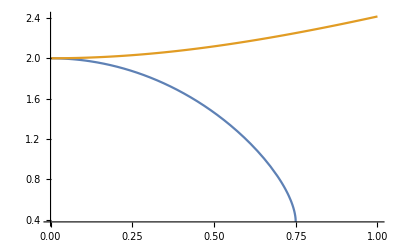

```mathematica
Plot[{-1+Sqrt[5-4Sqrt[1+m^2]]+2Sqrt[1+m^2]-2m^2,1+Sqrt[1+m^2]},{m,0,1}]
```

```mathematica
Series[-1+Sqrt[5-4Cosh[p]]+2Cosh[p]+2m Sinh[p],{p,0,6}]
```

2+2 m p+(m p^3)/3-p^4/2+(m p^5)/60-(7 p^6)/12+O[p]^7

```mathematica
Series[-1+Sqrt[5-4Sqrt[1+m^2]]+2Sqrt[1+m^2]-2m^2,{m,0,4}]
```

2-2 m^2-m^4/2+O[m]^5

```mathematica
Assuming[l>t&&l>0,Integrate[Sqrt[4Cosh[x]-5]/(m+Sinh[x])Exp[x t]/(Exp[l x]+1),{x,ArcCosh[5/4],Infinity}]]
```

∫_ArcCosh[5/4]^∞ (ⅇ^(t x) √(-5+4 Cosh[x]))/((1+ⅇ^(l x)) (m+Sinh[x]))ⅆx

```mathematica
Manipulate[Plot[{Sqrt[4Cosh[x]-5]/(m+Sinh[-x])Exp[-x t]/(Exp[-l x]+1),(2^t √3 √(x-Log[2]))/((1+2^l) (3/4+m))Exp[-(3/4+l-t)(x-Log[2])],(2^(2+l-t) √3 √(x-Log[2]))/((1+2^l) (-3+4 m))Exp[-(3/4+t)(x-Log[2])]},{x,ArcCosh[5/4],l},PlotRange->All],{m,0,1},{{t,l-1},0,l,1},{l,10,30,1}]
```

```mathematica
Assuming[l>t&&m>0,Integrate[(2^t √3 √(x-Log[2]))/((1+2^l) (3/4+m))Exp[-(3/4+l-t)(x-Log[2])],{x,Log[2],Infinity}]]//FullSimplify
```

(2^(4+t) √(3 π))/((1+2^l) (3+4 m) (3+4 l-4 t)^(3/2))

```mathematica
Assuming[l>t>0&&m>0,Integrate[(2^(2+l-t) √3 √(x-Log[2]))/((1+2^l) (-3+4 m))Exp[-(3/4+t)(x-Log[2])],{x,Log[2],Infinity}]]//FullSimplify
```

(2^(4+l-t) √(3 π))/((1+2^l) (-3+4 m) (3+4 t)^(3/2))

```mathematica
Series[Sqrt[4Cosh[x]-5]/(m+Sinh[-x])Exp[-x t]/(Exp[-l x]+1),{x,Log[2],1}]//FullSimplify
```

(2^(2+l-t) √3 √(x-Log[2]))/((1+2^l) (-3+4 m))+O[x-Log[2]]^(3/2)

```mathematica
Series[Sqrt[4Cosh[x]-5]/(m+Sinh[x])Exp[x t]/(Exp[l x]+1),{x,Log[2],1}]//FullSimplify
```

(2^t √3 √(x-Log[2]))/((1+2^l) (3/4+m))+O[x-Log[2]]^(3/2)

```mathematica
Exp@ArcCosh[5/4]//N
```

2.

```mathematica
D[Sqrt[4Cosh[x]-5]/(m+Sinh[x])Exp[x t]/(Exp[l x]+1),x]//FullSimplify
```

(ⅇ^(t x) (-(1+ⅇ^(l x)) Cosh[x] (-5+4 Cosh[x])-ⅇ^(l x) l (-5+4 Cosh[x]) (m+Sinh[x])+(1+ⅇ^(l x)) t (-5+4 Cosh[x]) (m+Sinh[x])+2 (1+ⅇ^(l x)) Sinh[x] (m+Sinh[x])))/((1+ⅇ^(l x))^2 √(-5+4 Cosh[x]) (m+Sinh[x])^2)

```mathematica
Assuming[m>0,Integrate[(m)/(m^2+p^2)Exp[I x p],{p,-Infinity,Infinity}]]//FullSimplify
```

ConditionalExpression[ⅇ^(-m Abs[x]) π, x∈ℝ]

```mathematica
Assuming[m>0&&x>0&&x∈Integers,Integrate[(m-I p)/(m^2+p^2)Exp[I x p],{p,-2Pi,2Pi}]Exp[m x]//FullSimplify]
```

ⅈ (ExpIntegralEi[(m-2 ⅈ π) x]-ExpIntegralEi[(m+2 ⅈ π) x])

```mathematica
finite[Lt_,p_,m_]:=Evaluate@Assuming[m>0&&p∈Reals,FullSimplify@Integrate[Exp[-m x]Exp[-I p x],{x,0,Lt/2}]]
```

```mathematica
(finite[Lt,p,m]+finite[Lt,-p,m])/2//FullSimplify
```

(m-ⅇ^(-(Lt m)/2) m Cos[(Lt p)/2]+ⅇ^(-(Lt m)/2) p Sin[(Lt p)/2])/(m^2+p^2)

```mathematica
Manipulate[ListLogLogPlot[Transpose@Table[{2Pi-(Im[-ExpIntegralEi[(m-2ⅈ π) x]+ExpIntegralEi[(m+2ⅈ π) x]]),1/Pi/x},{x,1,Lt,1}]],{m,0,1},{{Lt,20},0,60,1},{{ϵ,.2},0,1}]
```

```mathematica
Series[Cos[Lt m/2],{m,0,4}]
```

1-(Lt^2 m^2)/8+(Lt^4 m^4)/384+O[m]^5

```mathematica
Cosh[t-a]/Cosh[a]//FullSimplify
```

Cosh[a-t] Sech[a]

```mathematica
2/Pi^2//N
```

0.202642

```mathematica
Series[cP001[m,x,p]-cP003[m,x,p],{x,0,1}]//Simplify
Series[cP001[m,x,p],{x,0,1}]//Simplify
Series[cP003[m,x,p],{x,0,1}]//Simplify
```

(16 (-1+ⅇ^(2 ArcCosh[(3-2 Cos[p])/(2-2 Cos[p])])) m Cos[p/2] (-ⅇ^(2 ArcCosh[(3-2 Cos[p])/(2-2 Cos[p])])+m^2+ⅇ^ArcCosh[(3-2 Cos[p])/(2-2 Cos[p])] (1-m^2-5 ⅈ √(1/(5-4 Cos[p])))+(ⅇ^(2 ArcCosh[(3-2 Cos[p])/(2-2 Cos[p])])-m^2+4 ⅈ ⅇ^ArcCosh[(3-2 Cos[p])/(2-2 Cos[p])] √(1/(5-4 Cos[p]))) Cos[p]) Sin[p/2]^3 x)/(√(1/(5-4 Cos[p])) (-5+4 Cos[p]) ((-1+ⅇ^ArcCosh[(3-2 Cos[p])/(2-2 Cos[p])]) (ⅇ^ArcCosh[(3-2 Cos[p])/(2-2 Cos[p])]+m^2)+(-ⅇ^(2 ArcCosh[(3-2 Cos[p])/(2-2 Cos[p])])+m^2) Cos[p])^2)+O[x]^2

(2 ⅈ (-1+ⅇ^(2 ArcCosh[(3-2 Cos[p])/(2-2 Cos[p])])) (-1+Cos[p]) Sin[p])/(√(1/(5-4 Cos[p])) (-5+4 Cos[p]) (-(-1+ⅇ^ArcCosh[(3-2 Cos[p])/(2-2 Cos[p])]) (ⅇ^ArcCosh[(3-2 Cos[p])/(2-2 Cos[p])]+m^2)+(ⅇ^(2 ArcCosh[(3-2 Cos[p])/(2-2 Cos[p])])-m^2) Cos[p]))-(4 ⅈ ⅇ^ArcCosh[(3-2 Cos[p])/(2-2 Cos[p])] (-1+ⅇ^(2 ArcCosh[(3-2 Cos[p])/(2-2 Cos[p])])) m (-1+Cos[p]) Sin[p] x)/(((-1+ⅇ^ArcCosh[(3-2 Cos[p])/(2-2 Cos[p])]) (ⅇ^ArcCosh[(3-2 Cos[p])/(2-2 Cos[p])]+m^2)+(-ⅇ^(2 ArcCosh[(3-2 Cos[p])/(2-2 Cos[p])])+m^2) Cos[p])^2)+O[x]^2

-((8 ⅈ (-1+ⅇ^(2 ArcCosh[(3-2 Cos[p])/(2-2 Cos[p])])) Cos[p/2] Sin[p/2]^3)/(√(1/(5-4 Cos[p])) (-5+4 Cos[p]) (-(-1+ⅇ^ArcCosh[(3-2 Cos[p])/(2-2 Cos[p])]) (ⅇ^ArcCosh[(3-2 Cos[p])/(2-2 Cos[p])]+m^2)+(ⅇ^(2 ArcCosh[(3-2 Cos[p])/(2-2 Cos[p])])-m^2) Cos[p])))-(16 ((-1+ⅇ^(2 ArcCosh[(3-2 Cos[p])/(2-2 Cos[p])])) m Cos[p/2] Sin[p/2]^3) x)/(√(1/(5-4 Cos[p])) (-5+4 Cos[p]) (-(-1+ⅇ^ArcCosh[(3-2 Cos[p])/(2-2 Cos[p])]) (ⅇ^ArcCosh[(3-2 Cos[p])/(2-2 Cos[p])]+m^2)+(ⅇ^(2 ArcCosh[(3-2 Cos[p])/(2-2 Cos[p])])-m^2) Cos[p]))+O[x]^2

```mathematica
greens[{s,Ls},m,1]//FullSimplify//MatrixForm
```

(-(bb ⅇ^(-(2+Ls+s) α) (-1+ⅇ^(2 α)) (-2 b ⅇ^((1+Ls+2 s) α)+2 b ⅇ^(α+Ls α)+2 b ⅇ^(α+2 Ls α) m-2 b ⅇ^(α+2 s α) m+ⅇ^((2+Ls) α) (-1+m^2)-ⅇ^((Ls+2 s) α) (-1+m^2)))/(4 (2 b m Sinh[α]+(-1+m^2) Sinh[Ls α]+b (Sinh[(1+Ls) α]+m^2 Sinh[α-Ls α]))) | 0 | (ⅈ bb (-1+m^2) Sinh[α] Sinh[α-s α])/(2 b m Sinh[α]+(-1+m^2) Sinh[Ls α]+b (Sinh[(1+Ls) α]+m^2 Sinh[α-Ls α])) | 0
0 | -(bb ⅇ^(-(2+Ls+s) α) (-1+ⅇ^(2 α)) (-2 b ⅇ^((1+Ls+2 s) α)+2 b ⅇ^(α+Ls α)+2 b ⅇ^(α+2 Ls α) m-2 b ⅇ^(α+2 s α) m+ⅇ^((2+Ls) α) (-1+m^2)-ⅇ^((Ls+2 s) α) (-1+m^2)))/(4 (2 b m Sinh[α]+(-1+m^2) Sinh[Ls α]+b (Sinh[(1+Ls) α]+m^2 Sinh[α-Ls α]))) | 0 | (ⅈ bb (-1+m^2) Sinh[α] Sinh[α-s α])/(2 b m Sinh[α]+(-1+m^2) Sinh[Ls α]+b (Sinh[(1+Ls) α]+m^2 Sinh[α-Ls α]))
-(ⅈ bb (-1+m^2) Sinh[α] Sinh[α-s α])/(2 b m Sinh[α]+(-1+m^2) Sinh[Ls α]+b (Sinh[(1+Ls) α]+m^2 Sinh[α-Ls α])) | 0 | -(bb ⅇ^(-(2+Ls+s) α) (-1+ⅇ^(2 α)) (-2 b ⅇ^((1+Ls+2 s) α)+2 b ⅇ^(α+Ls α)+2 b ⅇ^(α+2 Ls α) m-2 b ⅇ^(α+2 s α) m+ⅇ^((2+Ls) α) (-1+m^2)-ⅇ^((Ls+2 s) α) (-1+m^2)))/(4 (2 b m Sinh[α]+(-1+m^2) Sinh[Ls α]+b (Sinh[(1+Ls) α]+m^2 Sinh[α-Ls α]))) | 0
0 | -(ⅈ bb (-1+m^2) Sinh[α] Sinh[α-s α])/(2 b m Sinh[α]+(-1+m^2) Sinh[Ls α]+b (Sinh[(1+Ls) α]+m^2 Sinh[α-Ls α])) | 0 | -(bb ⅇ^(-(2+Ls+s) α) (-1+ⅇ^(2 α)) (-2 b ⅇ^((1+Ls+2 s) α)+2 b ⅇ^(α+Ls α)+2 b ⅇ^(α+2 Ls α) m-2 b ⅇ^(α+2 s α) m+ⅇ^((2+Ls) α) (-1+m^2)-ⅇ^((Ls+2 s) α) (-1+m^2)))/(4 (2 b m Sinh[α]+(-1+m^2) Sinh[Ls α]+b (Sinh[(1+Ls) α]+m^2 Sinh[α-Ls α]))))

```mathematica
Δ[m,1]//FullSimplify
```

2 ⅇ^(α-Ls α) (2 b m Sinh[α]+(-1+m^2) Sinh[Ls α]+b (Sinh[(1+Ls) α]+m^2 Sinh[α-Ls α]))

```mathematica
gamma[[4]].pMinus.gamma[[4]]-pPlus//FullSimplify//MatrixForm
```

(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)